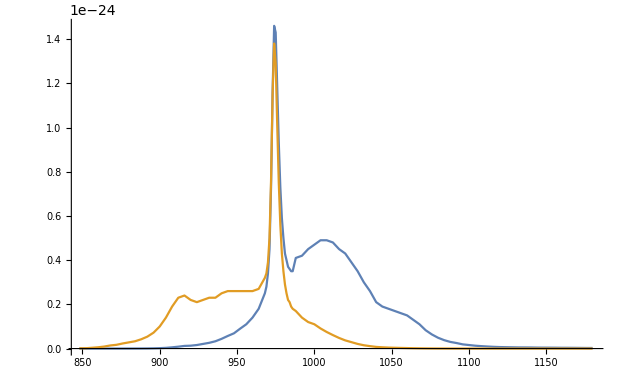

```mathematica
Clear["Global`*"]

(σ=Import[NotebookDirectory[]<>"CrossSection.xls"][[1,5;;,{12,15,16}]])//TableForm;

ListPlot[{σ[[All,{1,2}]],σ[[All,{1,3}]]},Joined->True,PlotRange->All]

σe=Interpolation[σ[[All,{1,2}]],InterpolationOrder->2];
σa=Interpolation[σ[[All,{1,3}]],InterpolationOrder->2];
```

```mathematica
c=3 10^8;(*м/с*)
τ=1.45 10^-3;(*с*)
NN=300;(*ppm*)
NN=6.62 10^22 NN;(*1/м^3*)
h=6.63 10^-34;(*Планк*)
Aeff=Pi/4 7^2 10^-12;(*Эффективная площадь моды*)

λp=960;(*нм*);
λs=1064;(*нм*)
Ps=Aeff h c/(λs 10^-9);
Pp=Aeff h c/(λp 10^-9);

L=2;

σp12=σa[λp];
σp21=σe[λp];
σp=σp12+σp21;
σs12=σa[λs];
σs21=σe[λs];
```

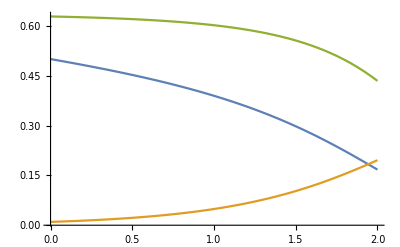

```mathematica
(*Усилитель*)
sol=NDSolve[{
0==ρp[z](σp12 N1[z]-σp21 N2[z])+ρs[z](σs12 N1[z]-σs21 N2[z])-N2[z]/τ,
ρs'[z]==ρs[z](σs21 N2[z]-σs12 N1[z]),
ρp'[z]==ρp[z](σp21 N2[z]-σp12 N1[z]),
N1[z]+N2[z]==NN, 
Pp ρp[0]==0.5,Ps ρs[0]==0.01
},{ρp,ρs,N1,N2},{z,0,L},AccuracyGoal->-15];

Plot[Evaluate[{Pp ρp[z],Ps ρs[z],N2[z]/NN}/.sol],{z,0,L},PlotRange->All]
```

```mathematica
(*Просветление среды*)
(*
Лецкия 4 Д.Мясников: 
1)13 слайд - инверсия в приближении слабого сигнала
2)20 слайд - условие просветления среды
enlightenment - просветление.
*)
```

```mathematica
σedisc=σ[[All,{1,2}]];
σadisc=σ[[All,{1,3}]];
n2enl=NN*σadisc/(2*(σadisc+σedisc));
n2enl[[All,1]]=σedisc[[All,1]];
ListPlot[n2enl,ImageSize->Large]
```

-Graphics-

```mathematica
eV=1.6021766208*10^-19;
μ=h*c/(λμ*10^-9)/eV;
modelFD=NN/2*1/(1+Exp[(μ-h*c/(λ*10^-9)/eV)/kT]);
fit=FindFit[n2enl,modelFD,{{λμ,1000},{kT,0.025}},λ]
λmin=Min[n2enl[[All,1]]];
λmax=Max[n2enl[[All,1]]];
Show[ListPlot[n2enl],Plot[modelFD/.fit,{λ,λmin,λmax},PlotStyle->Red],ImageSize->Large]
```

{λμ→972.507,kT→0.0250102}

-Graphics-

```mathematica
(*Мощность насыщения для LP01(~Гаусс)*)
```

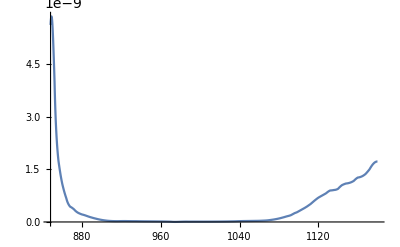

```mathematica
Psat[λ_]=Aeff*h*c/λ/(σa[λ]+σe[λ])/τ;
Plot[Psat[λ],{λ,λmin,λmax},PlotRange->All]
```

```mathematica
(* Усилитель, где изменением инверсии по z можно пренебречь, считать ее постоянной и заданной по всей длине*)
```

```mathematica
Clear[per]
```

```mathematica
sol=DSolve[{ρs'[z]==ρs[z]*(σe[λ]*N2-σa[λ]*(NN-N2)),Ps ρs[0]==P0s},ρs[z],{z,0,L}]
```

{{ρs[z]→1.39002×10^29 ⅇ^(1. N2 z InterpolatingFunction[{{848., 1180.}}, <>][λ]-1.986×10^25 z InterpolatingFunction[{{848., 1180.}}, <>][λ]+1. N2 z InterpolatingFunction[{{848., 1180.}}, <>][λ]) P0s}}

```mathematica
Manipulate[Plot[Ps ρs[z]/(P0s)/.sol/.λ->λs/.N2->NN*per/100,{z,0,L}],{per,1,30}]
```

```mathematica
Manipulate[Plot[Ps ρs[z]/(P0s)/.sol/.z->L/.N2->NN*per/100,{λ,λmin,λmax},PlotRange->All],{per,1,30}]
```

```mathematica
(*Построим дифференциальный коэффициент усиления*)
```

```mathematica
g[λ_]=(σe[λ]*N2-σa[λ]*(NN-N2));
Manipulate[Plot[g[λ]/.N2->NN*per/100,{λ,λmin,λmax},PlotRange->All],{per,0,100}]
```

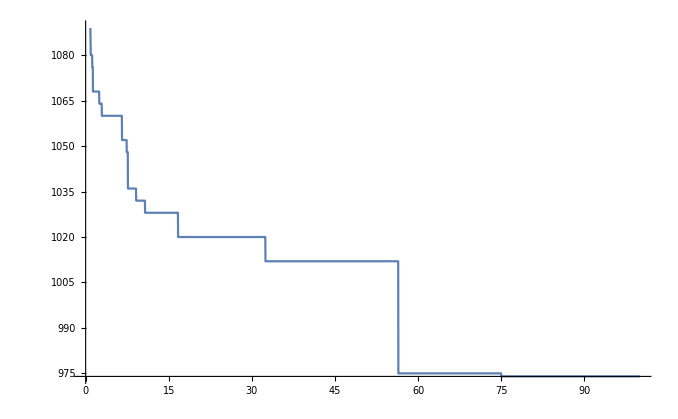

```mathematica
gdisc=(σedisc[[All,2]]*N2-σadisc[[All,2]]*(NN-N2))/.N2->NN*per/100;
Plot[σedisc[[Position[gdisc,Max[gdisc]][[1]],1]],{per,0,100}]
```

```mathematica
(*Слабый сигнал*)
```

```mathematica
(*k - коэффициент усиления,s - площадь жилы. Проинтегрировав уравнение для сигнала, получим след формулу:*)
```

```mathematica
k[λ_]:=Exp[N2TI*L*(σa[λ]+σe[λ])-NN*L*σa[λ]];
```

```mathematica
{t1,spectrk}=Timing[Manipulate[Plot[k[λ]/.(N2TI->NN*per/100),{λ,λmin,λmax},PlotRange->All],{{per,63},0,100}]];
spectrk
t1
```

0.00026

```mathematica
(*многократное решение скоростных уравнений*)
```

```mathematica
Ni=1000;
{t2,qwe}=Timing[spectrAmpl=Table[((Ps ρs[L]/(Ps ρs[0]))/.NDSolve[{
0==ρp[z](σp12 N1[z]-σp21 N2[z])-N2[z]/τ,
ρs'[z]==ρs[z](σe[λ] N2[z]-σa[λ] N1[z]),
ρp'[z]==ρp[z](σp21 N2[z]-σp12 N1[z]),
N1[z]+N2[z]==NN, 
Pp ρp[0]==0.5,Ps ρs[0]==0.000001
}/.λ->(λmin+i*(λmax-λmin)/Ni),{ρp,ρs,N1,N2},{z,0,L},AccuracyGoal->-15])[[1]],{i,0,Ni}]];
λdisc=Table[(λmin+i*(λmax-λmin)/Ni),{i,0,Ni}];
```

49.4725

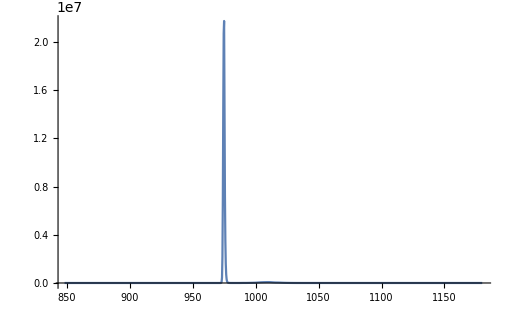

```mathematica
t2
ListLinePlot[Transpose[{λdisc,spectrAmpl}],PlotRange->All]
```

```mathematica
{t3,plot2}=Timing[Plot[(Ps ρs[L]/(Ps ρs[0]))/.NDSolve[{
0==ρp[z](σp12 N1[z]-σp21 N2[z])-N2[z]/τ,
ρs'[z]==ρs[z](σe[λ] N2[z]-σa[λ] N1[z]),
ρp'[z]==ρp[z](σp21 N2[z]-σp12 N1[z]),
N1[z]+N2[z]==NN, 
Pp ρp[0]==0.5,Ps ρs[0]==0.000001
}/.λ->λsig,{ρp,ρs,N1,N2},{z,0,L},AccuracyGoal->-15],{λsig,λmin,λmax},PlotRange->All]];
```

76.897

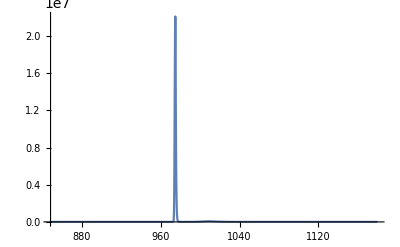

```mathematica
t3
plot2
```

```mathematica
(*Нормируем гауссов импульс*)
Es0=0.2*10^-9;
λFWHM=18;
λ0=1030;
δλ=λFWHM/2/Sqrt[Log[2]];
ρEs0[λ_]=Exp[-(λ-λ0)^2/δλ^2];
A0=Es0/(Aeff* h c/(λ0*10^-9)*Integrate[ρEs0[λ],{λ,-Infinity,Infinity}]);ρEs0[λ_]=ρEs0[λ]*A0*Aeff* h c/(λ0*10^-9);(*ρEs0[Дж/нм]*)
```

```mathematica
k[λ]/.N2TI->NN*per/100/.per->63
ρEsL[λ_]:=ρEs0[λ]*k[λ];

Manipulate[Plot[ρEsL[λ]/.{λ0->1030,N2TI->NN*per/100},{λ,λmin,λmax},PlotRange->All],{{per,63},0,100}]
```

ⅇ^(-3.972×10^25 InterpolatingFunction[{{848., 1180.}}, <>][λ]+2.50236×10^25 (InterpolatingFunction[{{848., 1180.}}, <>][λ]+InterpolatingFunction[{{848., 1180.}}, <>][λ]))

```mathematica
Clear[λm]
Manipulate[solλm=FindRoot[(ρEsL'[λm]==0)/.N2TI->NN*per/100/.per->63,{λm,λ01,1010,1040}],{{λ01,1018},1010,1040}]
```

```mathematica
λcgaus=λm/.solλm;
λleftgaus=λ/.FindRoot[ρEsL[λ]==1/2*ρEsL[λcgaus]/.N2TI->NN*per/100/.per->63,{λ,λcgaus,λcgaus-10,λcgaus}];
λrightgaus=λ/.FindRoot[ρEsL[λ]==1/2*ρEsL[λcgaus]/.N2TI->NN*per/100/.per->63,{λ,λcgaus+0.1,λcgaus+0.1,λcgaus+10}];
λFWHMgaus=λrightgaus-λleftgaus
```

12.357

```mathematica
ρEsL[λcgaus]/.{N2TI->NN*per/100}/.per->63
```

1.21311×10^-7

```mathematica
(*Нормируем прямоугольный спектр*)
```

```mathematica
ρErs0[λ_]=Es0/λFWHM*HeavisidePi[(λ-λ0)/λFWHM];
```

```mathematica
ρErsL[λ_]:=ρErs0[λ]*k[λ];
Manipulate[Plot[ρErsL[λ]/.{λ0->1030,N2TI->NN*per/100},{λ,λmin,λmax},PlotRange->All],{{per,63},0,100}]
```

```mathematica
Clear[λm]
Manipulate[solλm=FindRoot[(ρErsL'[λm]==0)/.N2TI->NN*per/100/.per->63,{λm,λ01,1020,1035}, AccuracyGoal->10],{{λ01,1020.999},1020,1035}]
```

```mathematica
λcrect=1021.000000000000001;
λleftrect=λcrect;
λrightrect=λ/.FindRoot[ρErsL[λ]==1/2*ρErsL[λcrect]/.N2TI->NN*per/100/.per->63,{λ,λcrect+0.1,λcrect+0.1,λcrect+10}]
λFWHMrect=λrightrect-λleftrect
```

1024.16

3.16345

```mathematica
(*Двойка*)
```

```mathematica
rCore=8.2/2;
rClad=125/2;
αdB=10;
αl=Log[10^(αdB/10/1000)];
GDMM=rCore^2/2/rClad^2;
AeffpDv=2*Pi*rClad^2*10^-12;
PpDv=AeffpDv h c/(λp 10^-9);
solDv=NDSolve[{
0==ρp[z](σp12 N1[z]-σp21 N2[z])+ρs[z](σs12 N1[z]-σs21 N2[z])-N2[z]/τ,
ρs'[z]==ρs[z](σs21 N2[z]-σs12 N1[z]-αl),
ρp'[z]==GDMM*ρp[z](σp21 N2[z]-σp12 N1[z])-αl*ρp[z],
N1[z]+N2[z]==NN, 
PpDv ρp[0]==100,Ps ρs[0]==0.01
},{ρp,ρs,N1,N2},{z,0,L},AccuracyGoal->-15];
Plot[ρs[z]/.solDv,{z,0,L},PlotRange->All]
```

-Graphics-